Payoffs and replicator expressions  (SI.1 - SI.8)

```mathematica
(*Clear Kernel of Unwanted Definitions*)
Quit[]
```

```mathematica
ClearAll["Global'*"]
```

```mathematica
(*To begin we first define the payoffs received by hosts and symbionts*)
(*x -> the proportion of a host's resource that is shared*)
(*α -> the exchange rate*)
(* γ -> matched efficiency *)
(* hγ -> mismatched efficiency *)
(* γg -> generalist host efficiency *)
pi=x*γ*α−x^2; (*Host matched payoff*)
pi2=x*hγ*α−x^2;(*Host mis-matched payoff*)
pig=x*γg*α−x^2;(*Generalist host payoff*)
ψ=x*γ*(1−α);(*Symbiont matched payoff*)
ψ2=x*hγ*(1−α);(*Host mis-matched payoff*)
ψg=x*γg*(1−α); (*Symbiont payoff from interaction with generalist host*)
```

```mathematica
(*v1 = frequency of host 1*)
(*v2 = frequency of host 2*)
S1 = v1*ψ+v2*ψ2+(1−v1−v2)*ψg;(*Symbiont 1 Average Payoff*)
S2 = v1*ψ2+v2*ψ+(1−v1−v2)*ψg;(*Symbiont 2 Average Payoff*)
S = Simplify[u*(1-u)*(S1-S2)];
(*Change in Symbiont Frequency over time*)
```

```mathematica
(*u = frequency of symbiont 1*)
H1=u*pi+(1-u)*pi2;(*Host 1 Average Payoff*)
H2 = u*pi2+(1−u)*pi;(*Host 2 Average Payoff*)
HG = pig;(*Generalist Host Average Payoff*)
Hbar = v1*H1+v2*H2+(1-v1-v2)(HG);(*Average payoff of a host selected at random*)
V1=Simplify[v1*(H1-Hbar)];(*Change in Host 1 frequency over time*)
V1/.{v1-> Subscript[v, 1],v2-> Subscript[v, 2],γg-> Subscript[γ, g]};
V2=Simplify[v2*(H2-Hbar)](*Change in Host 2 frequency over time*);
V2/.{v1-> Subscript[v, 1],v2-> Subscript[v, 2],γg-> Subscript[γ, g]};
```

First we find the equilibria of our system:

```mathematica
Solve[S==0,u]
Solve[V1 ==0,v1]
Solve[V2 ==0,v2]
```

{{u→0},{u→1}}

{{v1→0},{v1→(-hγ+hγ u+hγ u v2-u γ+v2 γ-u v2 γ+γg-v2 γg)/(-hγ+hγ u-u γ+γg)}}

{{v2→0},{v2→(hγ u-hγ v1+hγ u v1+γ-u γ-u v1 γ-γg+v1 γg)/(hγ u+γ-u γ-γg)}}

Equilibria given as ordered triples: (u, v, p). First boundary Equilibria are the generalist equilibria: (0,0,0) and (1,0,0)

There are other boundary equilibria:

```mathematica
v1s = (-hγ+hγ u+hγ u v2-u γ+v2 γ-u v2 γ+γg-v2 γg)/(-hγ+hγ u-u γ+γg);
v2s = (hγ u-hγ v1+hγ u v1+γ-u γ-u v1 γ-γg+v1 γg)/(hγ u+γ-u γ-γg);
Simplify[v2s /. {u -> 0, v1-> 0}]
Simplify[v2s /. {u -> 1, v1 -> 0}]
Simplify[v1s /. {u -> 0, v2 -> 0}]
Simplify[v1s /. { u -> 1, v2-> 0}]
(*Simplifying a host's internal equilibrium when two strategists are absent reveal additional boundary equilibria*)
```

1

1

1

«1 more identical outputs»

The remaining boundary equilibria are thus: 
Matched: (1,1,0) ,(0,0,1) and
Mismatched: (0,1,0)  (1,0,1)

We also considered internal equilibria:

```mathematica
Solve[v2s==0,u]
Solve[v1s==0,u]
v2intu0 = Simplify[v2s /.  u-> 0];
Collect[v2intu0, v1]
v2intu1= Simplify[v2s /. u -> 1];
Collect[v2intu1, v1] 

v1intu0= Simplify[v1s /. u -> 0];
Collect[v1intu0, v2]

v1intu1= Simplify[v1s /. u -> 1];
Collect[v1intu1, v2]
```

{{u→(hγ v1-γ+γg-v1 γg)/((1+v1) (hγ-γ))}}

{{u→(hγ-v2 γ-γg+v2 γg)/((1+v2) (hγ-γ))}}

1+(v1 (-hγ+γg))/(γ-γg)

1+(v1 (-γ+γg))/(hγ-γg)

1+(v2 (-γ+γg))/(hγ-γg)

1+(v2 (-hγ+γg))/(γ-γg)

We linearize this system by constructing the jacobian matrix:

```mathematica
J =({{D[S,u], D[S,v1], D[S,v2]}, {D[V1,u], D[V1,v1], D[V1,v2]}, {D[V2,u], D[V2,v1], D[V2,v2]}});
```

We then evaluate the sign of eigenvalues corresponding to the jacobian evaluated at the boundary equilibria:

```mathematica
(*Generalist Equilibria*)
Eigenvalues[J/.{u -> 0,v1->  0,v2-> 0}]
Eigenvalues[J/.{u -> 1,v1->  0,v2-> 0} ]
```

{0,x α (hγ-γg),x α (γ-γg)}

{0,x α (hγ-γg),x α (γ-γg)}

```mathematica
(*Matched Equilibria*)
Eigenvalues[J/.{u -> 1,v1->  1,v2-> 0} ]
Eigenvalues[J/.{u -> 0,v1->  0,v2-> 1} ]
```

{-x (-1+α) (hγ-γ),x α (hγ-γ),-x α (γ-γg)}

{-x (-1+α) (hγ-γ),x α (hγ-γ),-x α (γ-γg)}

```mathematica
(*Mismatched Equilibria*)
Eigenvalues[J/.{u -> 1,v1->  0,v2-> 1} ]
Eigenvalues[J/.{u -> 0,v1->  1,v2-> 0} ]
```

{x (-1+α) (hγ-γ),-x α (hγ-γ),-x α (hγ-γg)}

{x (-1+α) (hγ-γ),-x α (hγ-γ),-x α (hγ-γg)}

Internal equilibrium at (0.5,0.5,0.5). We evaluated the eigenvalues at this point:

```mathematica
Eigenvalues[J/.{u -> 1/2,v1->  1/2,v2-> 1/2} ]
```

{-1/2 ⅈ x √(-1+α) √α (hγ-γ),1/2 ⅈ x √(-1+α) √α (hγ-γ),-1/2 x α (hγ+γ-2 γg)}

This point is a saddle.

Finally, we consider the case of absent generalists, and any symbiont frequency:

```mathematica
Eigenvalues[J/.{u -> u,v1->  0,v2-> 0} ]
```

{0,x α (hγ u+γ-u γ-γg),-x α (-hγ+hγ u-u γ+γg)}

Stability at this point was determined using the theory of bifurcation without parameters.

```mathematica
(* Dynamics d[u,v1,v2]/dt = F shifted to the right end point of the interval *)
F={S,V1,V2}/.{u-> u+1-(pi-pig)/(pi-pi2)};
```

```mathematica
(* The Jacobian in the desired form *)
J=Simplify[D[F,{{u,v1,v2}}]/.{u-> 0,v1-> 0,v2->0}];
```

```mathematica
(* Reduce system *)
EQ=F/.{u-> μ,v1-> y,v2-> z};
m=a20*μ^2+a11*μ*y+a02*y^2;
IC=D[m,{{μ,y}}].EQ[[1;;2]]-EQ[[3]]/.{z-> m};
```

```mathematica
Q1=Coefficient[IC/.{y->0},μ^2];
Q2=Coefficient[IC,μ*y];
Q3=Coefficient[IC/.{μ->0},y^2];
Solve[{Q1==0,Q2==0,Q3==0},{a11,a02,a20}]
```

{{a11→0,a02→0,a20→0}}

```mathematica
(* The reduced system *)
G=Simplify[EQ[[1;;2]]/.{z->0}]
```

{-(x y (-1+α) (hγ-γg+hγ μ-γ μ) (γ-γg+hγ μ-γ μ))/(hγ-γ),x (-1+y) y α (hγ-γ) μ}

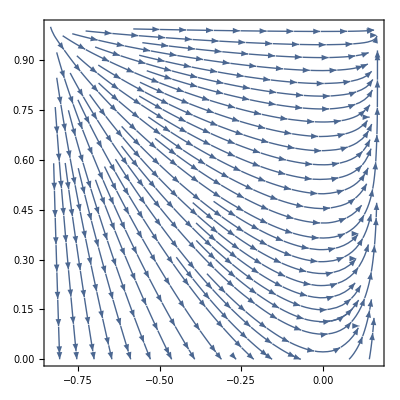

```mathematica
(* Example plotted vector field *)
VF =G/.{α->0.5,γ->1.1,γg->1,hγ-> 0.5,x->0.5}; 
(* bifuction point at right endpoint of interval *)
 μ2 = 1-(pi-pig)/(pi-pi2)/.{α->0.5,γ->1.1,γg->1,hγ-> 0.5,x->0.5} ;
StreamPlot[VF[[1;;2]],{μ,-μ2,1-μ2},{y,0,1}]
```